# MATH 263 Numerical differential equations

Ethan Smith

## Lecture 3: Error analysis and Heun’s method 18 FEB 2021

## Assigned reading for next time.

Zill, Section 9.2.

## Method implementations.

```mathematica
euler[f_,a_,b_,y0_,n_]:=Module[{x,y,h},
{x[0],y[0]} = {a,y0};
h=N[(b-a)/n];
Do[
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*f[x[i],y[i]];,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

```mathematica
heun[f_,a_,b_,y0_,n_]:=Module[{x,y,h},
{x[0],y[0]} = {a,y0};
h=N[(b-a)/n];
Do[
x[i+1]=x[i]+h;
y[i+1]=y[i]+h*(f[x[i],y[i]]+f[x[i+1],y[i]+h*f[x[i],y[i]]])/2;,
{i,0,n-1}
];
Return[Table[{x[i],y[i]},{i,0,n}]]
];
```

## Error analysis.

### General concepts.

In general, numerical methods suffer from two distinct sources of error.

Rounding error is error introduced due to the use of finite precision arithmetic.  Though important, we will largely ignore this type of error in this course.  Mathematica’s somewhat opaque data types make this difficult to analyze anyway.

Truncation error (or discretization error) is the error introduced by explicit approximations made in the method.  This error would remain present even if all arithmetic were performed exactly.

Truncation error can be discussed in two different forms.

Global truncation error in the (i+1)st step is the difference between the the true solution value and the computed solution, i.e., it is the quantity

e_(i+1) = y(x_(i+1)) - y_(i+1) ,

where y is the true solution to the given IVP and y_i is the computed (approximate) solution.

Local truncation error is the error made in just one step of the method.  In particular, we assume that the previous computed value y_(i-1) is exactly correct and compute the error at the next step, i.e., it is the quantity

l_(i+1) = y_*(x_(i+1))- y_(i+1) ,

where y_* is the true solution to the ODE that passes through the point (x_i,y_i), but not necessarily to the given IVP.  Put another way, the local truncation error is the extent to which the true solution fails to satisfy the formula the method uses to produce the (i+1)st approximation.

For any reasonable method, both types of error should tend to zero as the step size h = x_(i+1)-x_i tends to zero.  So, we are usually interested in bounding errors as a function of h.  We say that the error E is O(h^p) if |E| ≤ C h^p for some positive constant C.  In the typical situation, h is small, and so larger values of p are preferred.  (Note: Near zero, h^3 “dies faster” than h^2, which itself “dies faster” than h.)  In many situations, if the local truncation error is O(h^(p+1)), then the global truncation error is O(h^p).  Since local truncation error is easier to analyze, we will focus our attention on local error.

### Analysis of Euler’s method.

Consider the first order IVP

y’=f(x,y), y(x_0) = y_0.

We now analyze the local truncation error for Euler’s method assuming that the true solution has a continuous 2nd derivative.    In particular, we have

y_(i+1)=y_i+h f(x_i,y_i),

where h=x_(i+1)-x_i and we assume that y_i = y(x_i) exactly.  Thus, by Taylor’s theorem with remainder, there is a c∈ (x_i,x_(i+1)) so that

y(x_(i+1)) = y(x_i) + y'(x_i)(x_(i+1)-x_i) + (y''(c))/(2!)(x_(i+1)-x_i)^2 
	   = y_i + f(x_i, y_i) h +(y''(c))/2 h^2.

Therefore, the absolute local truncation error at step i+1 is

|l_(i+1)|= |y(x_(i+1)) - y_(i+1)| = h^2/2|y''(c)| ≤ M/2 h^2,

where M = max {|y''(x)| : x∈(x_i,x_(i+1))} exists (and is finite).  (Note: We know that M is finite since we assumed that y'' is continuous.  Thus, we have shown that the local truncation error for Euler’s method is O(h^2), which means that the global truncation error is O(h).

## A modified (improved) Euler method.

We consider again the problem of numerically approximating the solution to the first order IVP

y’=f(x,y), y(x_0) = y_0.

Assuming that the true solution y to the first order IVP has 3 continuous derivatives (i.e., y', y'', y''' all exist and are continuous), we now develop a modified/improved Euler method, which is also known as Heun’s method.  It is an example of an 2nd order Runge-Kutta method which we will discuss later.  (Note: This derivation differs from Zill, and is better for building understanding.)  By Taylor’s theorem (with remainder), we have

y(x_(i+1)) = y(x_i) + y'(x_i)(x_(i+1)-x_i) + (y''(x_i))/(2!)(x_(i+1)-x_i)^2 + (y'''(c))/(3!)(x_(i+1)-x_i)^3

for some c∈ (x_i,x_(i+1)).  Assuming y(x_i)=y_i and that h = x_(i+1) - x_i is small, we throw away (truncate) the last term on the right, and arrive at the approximation

y(x_(i+1)) ≈ y_i + y'(x_i)h + (y''(x_i))/(2!)h^2.

Because the true solution must satisfy the ODE, we have y'(x_i) = f(x_i,y_i) just as for the original Euler method, but unfortunately the ODE contains no information about the second derivative y''(x_i).  Actually, this is a lie, but we would need calc III ideas to unpack the information and we don’t really want the exact information anyway.  Instead, we approximate using the definition of derivative.  In particular,

y''(x_i) =  lim__(x_(i+1)→x_i)(y'(x_(i+1)) - y'(x_i))/(x_(i+1)-x_i) 
 ≈(y'(x_(i+1)) - y'(x_i))/(x_(i+1)-x_i) 
                     =(f(x_(i+1),y(x_(i+1))) -f(x_i,y_i))/h .

Substituting this information into (1), we have

y(x_(i+1)) ≈ y_i + f(x_i,y_i)h + (f(x_(i+1),y(x_(i+1))) -f(x_i,y_i))/2 h
	 = y_i +(f(x_(i+1),y(x_(i+1))) + f(x_i,y_i))/2 h.

At this point, we would like to just define the approximation y_(i+1) to be the right-hand side above, but unfortunately, it still depends on y(x_(i+1)).  We alleviate this concern by approximating the value of y(x_(i+1)) on the right-hand side by the original Euler approximation y_i + h f(x_i,y_i).   (Note: More rigorous derivation is possible by appealing to the multivariable Taylor series for f(x,y).)  Thus, our modified algorithm puts

y_(i+1) = y_i +(f(x_(i+1),y_i+h f(x_i,y_i)) + f(x_i,y_i))/2 h,

It can be shown that the local truncation error for this method is O(h^3), and hence the global truncation error is O(h^2).

Consider the IVP y' = x+y, y(0)=1.

Compute the exact solution to the IVP.

```mathematica
f[x_,y_]=x+y;
{x0,y0}={0,1};
{a,b}={0,1};
Y[x_]=y[x]/.DSolve[{y'[x]==f[x,y[x]],y[x0]==y0}, y[x], x][[1]];
Print[StringForm["The exact solution to the IVP ``, `` is ``.",TraditionalForm[y'==f[x,y]],TraditionalForm[y[x0]==y0],TraditionalForm[y[x]==Y[x]]]];
```

The exact solution to the IVP y'==x+y, y(0)==1 is y(x)==-x+2 ⅇ^x-1.

Compute numerical solutions to the IVP over the interval [0,1] using both the Euler method and Heun’s method with n=10 steps.  Plot the two numerical solutions together with the true solution on a single set of axes.

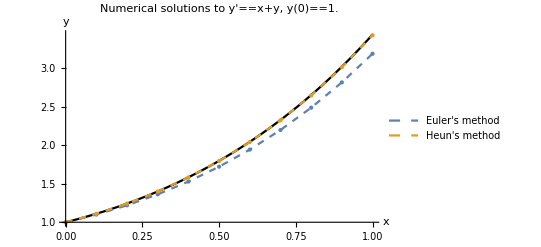

```mathematica
n=10;
em10=euler[f,a,b,y0,n];
heun10=heun[f,a,b,y0,n];
Show[
Plot[Y[x],{x,a,b},PlotStyle->Black],
ListPlot[{em10,heun10},PlotStyle->{{PointSize[Large],Dashed}},Joined->True,Mesh->All,PlotLegends->{"Euler's method","Heun's method"}],AxesLabel->{"x","y"},PlotLabel->StringForm["Numerical solutions to ``, ``.", TraditionalForm[y'==f[x,y]],TraditionalForm[y[x0]==y0]]
]
```

Create a table of absolute and relative errors at x=1 for each method with n=10, 100, 1000 steps.

```mathematica
numSteps={10,100,1000};

ynEuler = Table[Last[euler[f,a,b,y0,n]][[2]],{n,numSteps}];
eulerErrors={numSteps,Abs[ynEuler-Y[1]],Abs[ynEuler/Y[1]-1]};

Labeled[TableForm[eulerErrors,TableDirections->Row,TableHeadings->{{"n", "|y(1)-y_n|", "|y(1)-y_n|/|y(1)|"},None}],"Euler's method",Top]

ynHeun = Table[Last[heun[f,a,b,y0,n]][[2]],{n,numSteps}];
heunErrors={numSteps,Abs[ynHeun-Y[1]],Abs[ynHeun/Y[1]-1]};

Labeled[TableForm[heunErrors,TableDirections->Row,TableHeadings->{{"n", "|y(1)-y_n|", "|y(1)-y_n|/|y(1)|"},None}],"Heun's method",Top]
```

n | |y(1)-y_n| | |y(1)-y_n|/|y(1)|
10 | 0.249079 | 0.072479
100 | 0.026936 | 0.00783806
1000 | 0.00271579 | 0.000790264Euler's method

n | |y(1)-y_n| | |y(1)-y_n|/|y(1)|
10 | 0.00840196 | 0.00244487
100 | 0.0000899318 | 0.0000261691
1000 | 9.05415×10^-7 | 2.63465×10^-7Heun's method